# Variance

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dir ="../AnalysisData/best_categ_pass_agent/";
```

```mathematica
ba1=Import[StringJoin[dir,"B_avoid_n1.dat"]];
ba2=Import[StringJoin[dir,"B_avoid_n2.dat"]];
ba3=Import[StringJoin[dir,"B_avoid_n3.dat"]];
ba4=Import[StringJoin[dir,"B_avoid_n4.dat"]];
ba5=Import[StringJoin[dir,"B_avoid_n5.dat"]];
bc1=Import[StringJoin[dir,"B_catch_n1.dat"]];
bc2=Import[StringJoin[dir,"B_catch_n2.dat"]];
bc3=Import[StringJoin[dir,"B_catch_n3.dat"]];
bc4=Import[StringJoin[dir,"B_catch_n4.dat"]];
bc5=Import[StringJoin[dir,"B_catch_n5.dat"]];
```

```mathematica
max = 0.25
```

0.25

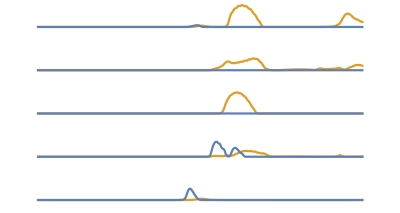

ObjectRecogVar.eps

```mathematica
GraphicsColumn[
{
Show[{
ListLinePlot[Variance[bc1],PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[ba1],PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[bc2],PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[ba2],PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[bc3],PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[ba3],PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[bc4],PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[ba4],PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[bc5],PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[ba5],PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
Export["ObjectRecogVar.eps",%]
```

```mathematica
Variance[Flatten[ac1]]
```

0.00693533

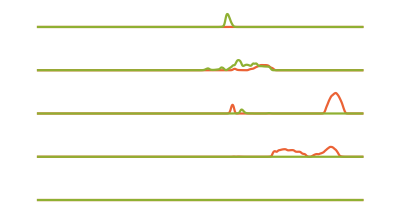

PerceiveVar.eps

```mathematica
GraphicsColumn[
{
Show[{
ListLinePlot[Variance[ac1],PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[aa1],PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[ac2],PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[aa2],PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[ac3],PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[aa3],PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[ac4],PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[aa4],PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[Variance[ac5],PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[Variance[aa5],PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,max}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
Export["PerceiveVar.eps",%]
```

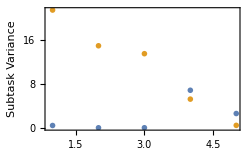

TotalVar.eps

```mathematica
ListPlot[{{Total[Variance[ba1]],Total[Variance[ba2]],Total[Variance[ba3]],Total[Variance[ba4]],Total[Variance[ba5]]},
{Total[Variance[bc1]],Total[Variance[bc2]],Total[Variance[bc3]],Total[Variance[bc4]],Total[Variance[bc5]]}},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Subtask Variance"},ImageSize->250,PlotMarkers->{●,●}]
Export["TotalVar.eps",%]
```

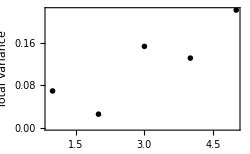

TotalCombinedVar.eps

```mathematica
ListPlot[
{Variance[Flatten[Catenate[{ba1,bc1}]]],Variance[Flatten[Catenate[{ba2,bc2}]]],Variance[Flatten[Catenate[{ba3,bc3}]]],Variance[Flatten[Catenate[{ba4,bc4}]]],Variance[Flatten[Catenate[{ba5,bc5}]]]}
,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
Export["TotalCombinedVar.eps",%]
```

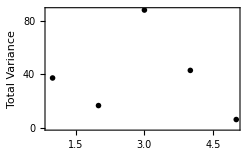

TotalCombinedVar.eps

```mathematica
ListPlot[
{Total[Variance[Catenate[{ba1,bc1}]]],Total[Variance[Catenate[{ba2,bc2}]]],Total[Variance[Catenate[{ba3,bc3}]]],Total[Variance[Catenate[{ba4,bc4}]]],Total[Variance[Catenate[{ba5,bc5}]]]}
,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
Export["TotalCombinedVar.eps",%]
```

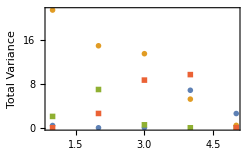

TotalVar.eps

```mathematica
ListPlot[{{Total[Variance[ba1]],Total[Variance[ba2]],Total[Variance[ba3]],Total[Variance[ba4]],Total[Variance[ba5]]},
{Total[Variance[bc1]],Total[Variance[bc2]],Total[Variance[bc3]],Total[Variance[bc4]],Total[Variance[bc5]]},
{Total[Variance[aa1]],Total[Variance[aa2]],Total[Variance[aa3]],Total[Variance[aa4]],Total[Variance[aa5]]},
{Total[Variance[ac1]],Total[Variance[ac2]],Total[Variance[ac3]],Total[Variance[ac4]],Total[Variance[ac5]]}},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotMarkers->{●,●,■,■}]
Export["TotalVar.eps",%]
```

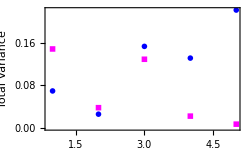

TotalCombinedVar.eps

```mathematica
ListPlot[{
{Variance[Flatten[Catenate[{ba1,bc1}]]],Variance[Flatten[Catenate[{ba2,bc2}]]],Variance[Flatten[Catenate[{ba3,bc3}]]],Variance[Flatten[Catenate[{ba4,bc4}]]],Variance[Flatten[Catenate[{ba5,bc5}]]]},
{Variance[Flatten[Catenate[{aa1,ac1}]]],Variance[Flatten[Catenate[{aa2,ac2}]]],Variance[Flatten[Catenate[{aa3,ac3}]]],Variance[Flatten[Catenate[{aa4,ac4}]]],Variance[Flatten[Catenate[{aa5,ac5}]]]}
},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotStyle->{Blue,Magenta},PlotMarkers->{●,■}]
Export["TotalCombinedVar.eps",%]
```

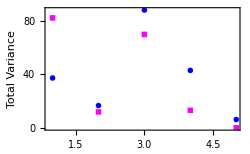

TotalCombinedVar.eps

```mathematica
ListPlot[{
{Total[Variance[Catenate[{ba1,bc1}]]],Total[Variance[Catenate[{ba2,bc2}]]],Total[Variance[Catenate[{ba3,bc3}]]],Total[Variance[Catenate[{ba4,bc4}]]],Total[Variance[Catenate[{ba5,bc5}]]]},
{Total[Variance[Catenate[{aa1,ac1}]]],Total[Variance[Catenate[{aa2,ac2}]]],Total[Variance[Catenate[{aa3,ac3}]]],Total[Variance[Catenate[{aa4,ac4}]]],Total[Variance[Catenate[{aa5,ac5}]]]}
},PlotRange->All,Frame->True,FrameLabel->{"Neuron","Total Variance"},ImageSize->250,PlotStyle->{Blue,Magenta},PlotMarkers->{●,■}]
Export["TotalCombinedVar.eps",%]
```

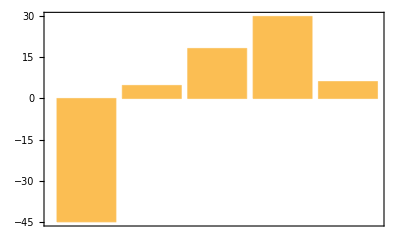

```mathematica
BarChart[{Total[Variance[Catenate[{ba1,bc1}]]]-Total[Variance[Catenate[{aa1,ac1}]]],Total[Variance[Catenate[{ba2,bc2}]]]-Total[Variance[Catenate[{aa2,ac2}]]],
Total[Variance[Catenate[{ba3,bc3}]]]-Total[Variance[Catenate[{aa3,ac3}]]],Total[Variance[Catenate[{ba4,bc4}]]]-Total[Variance[Catenate[{aa4,ac4}]]],Total[Variance[Catenate[{ba5,bc5}]]]-Total[Variance[Catenate[{aa5,ac5}]]]},Frame->True]
```